```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

C0=(m^(3/2) n0 Gamma[κ])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κ) Gamma[-1/2+κ])


assumps={κ>3/2,Tpar0>0,Tperp0>0, B>0,B0>0,A0>0,m>0,ΔPE∈Reals,n0>0,d>0};

FullSimplify[C0*2*Pi*Integrate[vperp*(1+(m*vpar^2)/(2*κ*Tpar0)+ ((m*vperp^2)*(A0+(1-A0)*d))/(2*κ*Tperp0)+ΔPE/(κ*Tpar0))^(-(κ+1)),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps],assumps]
```

(m^(3/2) n0 Gamma[κ])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κ) Gamma[-1/2+κ])

ConditionalExpression[(n0 ((Tpar0 κ)/(ΔPE+Tpar0 κ))^(-1/2+κ))/(A0+d-A0 d), ΔPE≥0||ΔPE+Tpar0 κ≥0]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={Tpar0>0,ΔPE∈Reals};

Limit[(ΔPE/(Tpar0*κ)+1)^(1/2-κ),κ->Infinity,Assumptions->assumps]
Limit[(ΔPE/(Tpar0*κ)+1)^(-1/2-κ),κ->Infinity,Assumptions->assumps]
```

ⅇ^(-ΔPE/Tpar0)

ⅇ^(-ΔPE/Tpar0)

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*contrary to before d = B/B0>1*)
assumps={Tpar>0,Tperp>0,A>0,κpar>0.5,κperp>1,λ>0,d>1,ΔPE∈Reals,ΔPE/(κpar*Tpar)>-1,n0>0}
x=λ*A*(d-1)/(ΔPE/(κpar*Tpar)+1);
f=n0*d*(ΔPE/(κpar*Tpar)+1)^(-1/2-κpar)*(λ/(λ+1.5))*Hypergeometric2F1[1,κpar+0.5,κpar+κperp+1.5,1-λ*A*(d-1)/(ΔPE/(κpar*Tpar)+1)]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*contrary to before d = B/B0>1*)
assumps={Tpar>0,Tperp>0,A>0,κpar>0.5,κperp>1,λ>0,d>1,ΔPE∈Reals,ΔPE/(κpar*Tpar)>-1,n0>0}
Integrate[]
```

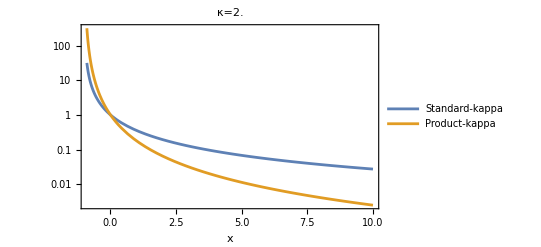
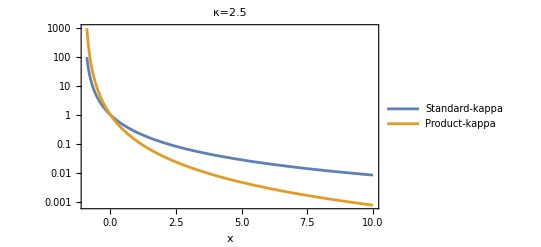
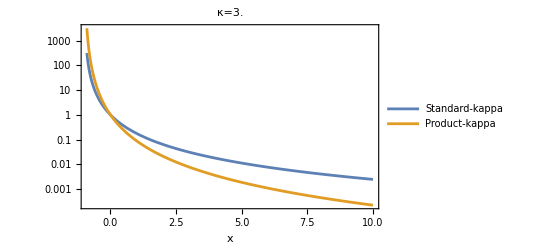
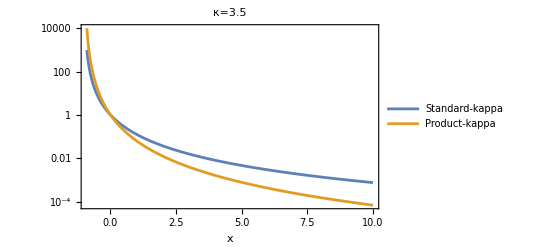
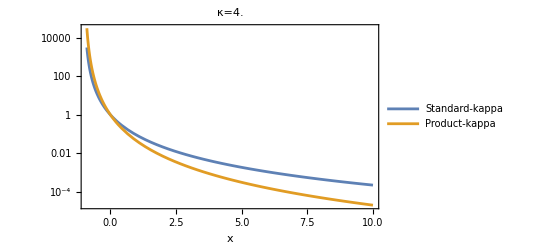
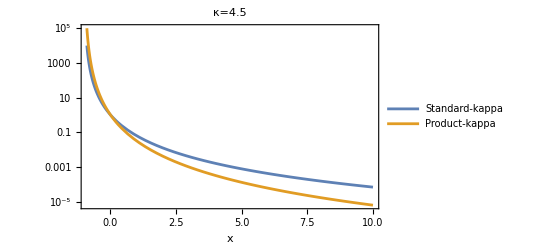
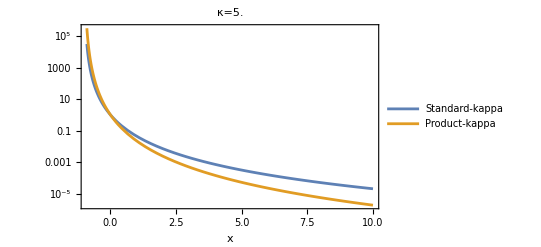
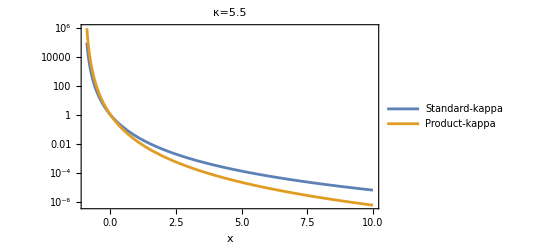

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
Table[LogPlot[{(1+x)^(1/2-κ),(1+x)^(-1/2-κ)},{x,-0.9,10},Frame->True,FrameLabel->{"x",""},PlotLabel->"κ="<>ToString[κ],PlotLegends->{"Standard-kappa","Product-kappa"}],{κ,2,10,0.5}]
```

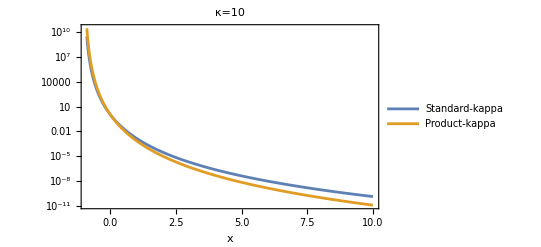
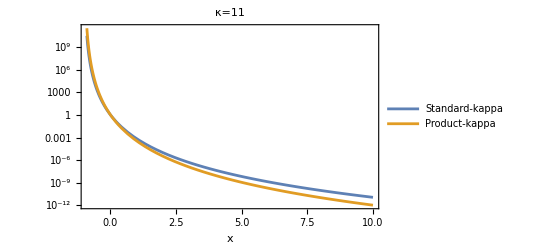
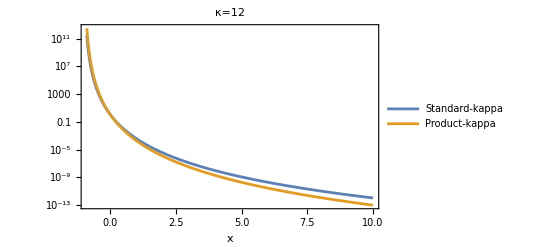
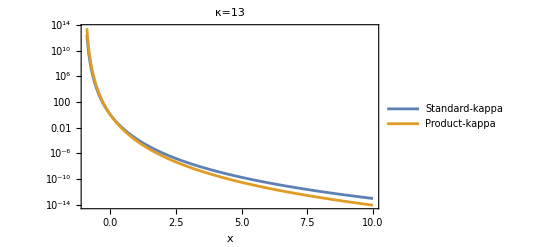
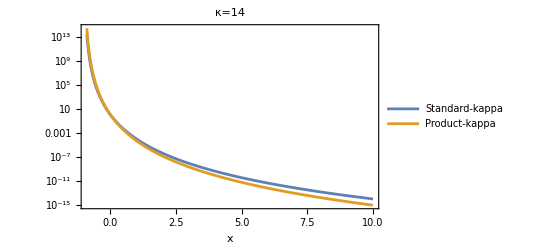
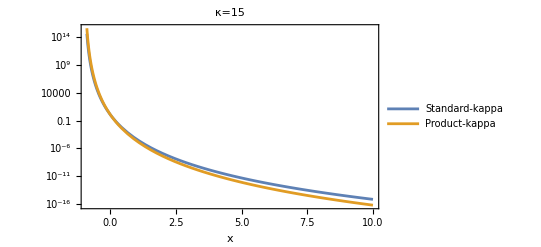
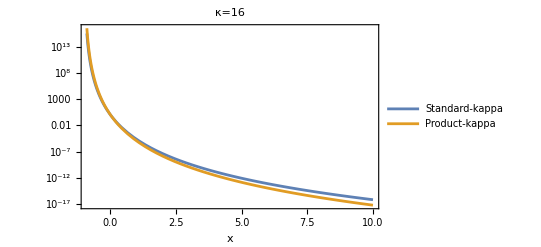
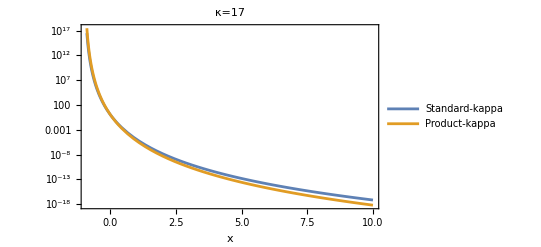

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
Table[LogPlot[{(1+x)^(1/2-κ),(1+x)^(-1/2-κ)},{x,-0.9,10},Frame->True,FrameLabel->{"x",""},PlotLabel->"κ="<>ToString[κ],PlotLegends->{"Standard-kappa","Product-kappa"}],{κ,10,20,1}]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
a=Table[(1+x)^(1/2-κ)/(1+x)^(-1/2-κ),{x,-0.9,10,0.1},{κ,2,100,1}];
Dimensions[a]
Max[a[[All,1]]]
Min[a[[All,1]]]
Max[a[[All,19]]]
Min[a[[All,19]]]
Max[a[[All,29]]]
Min[a[[All,29]]]
Max[a[[All,39]]]
Min[a[[All,39]]]
Max[a[[All,99]]]
Min[a[[All,99]]]
```

{110,99}

11.

0.1

11.

0.1

11.

0.1

11.

0.1

11.

0.1

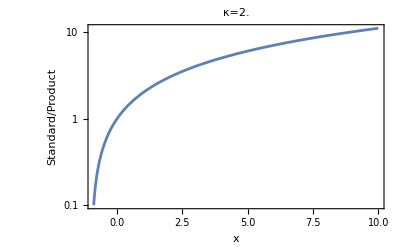
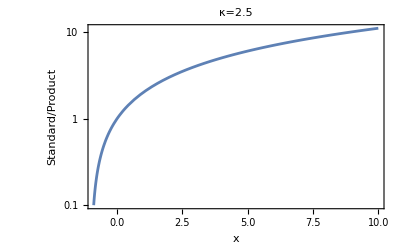
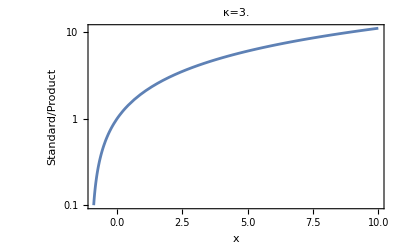
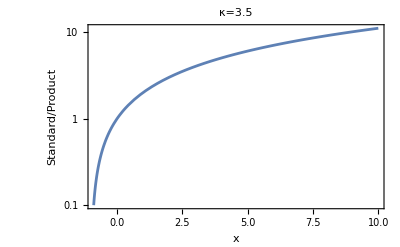
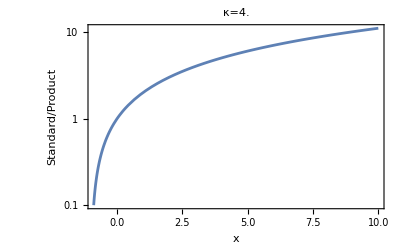
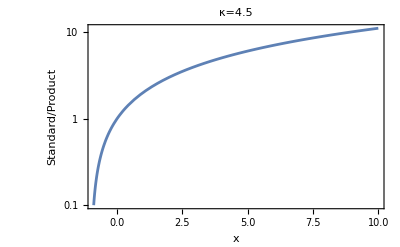
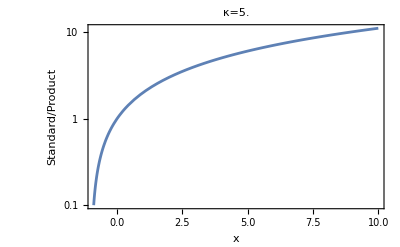
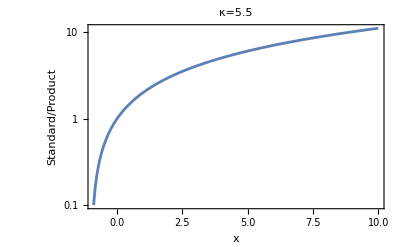

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
Table[LogPlot[(1+x)^(1/2-κ)/(1+x)^(-1/2-κ),{x,-0.9,10},Frame->True,FrameLabel->{"x","Standard/Product"},PlotLabel->"κ="<>ToString[κ]],{κ,2,10,0.5}]
```

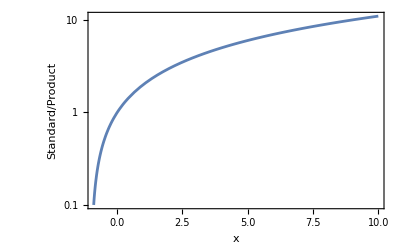

```mathematica
LogPlot[(1+x),{x,-0.9,10},Frame->True,FrameLabel->{"x","Standard/Product"}]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*contrary to before now we have, d = B/B0>1*)
assumps={Tpar0>0,A0>0,κpar0>0.5,λ0*κpar0>1,λ0>0,d>1,ΔPE∈Reals,ΔPE/(κpar0*Tpar0)>-1,n0>0,m>0};
(*assumps={Tpar>0,A>0,κpar>0.5,λ*κpar>1,λ>0,d>1,ΔPE∈Reals,ΔPE/(κpar*Tpar)>-1,n0>0,m>0};*)
(*assumps={m>0,κpar>0.5,λ>0,λ*κpar>1,A>0,Tpar>0}*)
(*x=λ*A*(d-1)/(ΔPE/(κpar*Tpar)+1);*)
(*f=c*(1+(m*vperp^2)/(2*κperp*Tperp))^(-1-κperp)*(1+(m*vpar^2)/(2*κpar*Tpar))^(-1-κpar)*)
(*f=c*(1+(m*vperp^2)/(2*A*λ*κpar*Tpar))^(-1-λ*κpar)*(1+(m*vpar^2)/(2*κpar*Tpar))^(-1-κpar)*)
(*FullSimplify[Solve[n==2*Pi*Integrate[vperp*c*(1+(m*vperp^2)/(2*A*λ*κpar*Tpar))^(-1-λ*κpar)*(1+(m*vpar^2)/(2*κpar*Tpar))^(-1-κpar),{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],c,Assumptions->assumps],assumps]*)
(*c->(n Gamma[1+κpar])/(2 √2 A π^(3/2) √((Tpar^3 κpar)/m^3) Gamma[1/2+κpar])*)

(*f=(n Gamma[1+κpar])/(2 √2 A π^(3/2) √((Tpar^3 κpar)/m^3) Gamma[1/2+κpar])*(1+(m*vperp^2)/(2*A*λ*κpar*Tpar))^(-1-λ*κpar)*(1+(m*vpar^2)/(2*κpar*Tpar))^(-1-κpar);*)



(*n=n0*d*(ΔPE/(κpar*Tpar)+1)^(-1/2-κpar)*(λ/(λ+1.5))*Hypergeometric2F1[1,κpar+0.5,κpar*(1+λ)+1.5,1-λ*A*(d-1)/(ΔPE/(κpar*Tpar)+1)]*)

(*f0=(n0 Gamma[1+κpar0])/(2 √2 A0 π^(3/2) √((Tpar0^3 κpar0)/m^3) Gamma[1/2+κpar0])*(1+(m*vperp^2)/(2*d*A0*λ0*κpar0*Tpar0))^(-1-λ0*κpar0)*(1+(m*vpar^2/2+m*vperp^2/2*(1-1/d)+ΔPE)/(κpar0*Tpar0))^(-1-κpar0);*)

FullSimplify[n0*d*(ΔPE/(κpar0*Tpar0)+1)^(-1/2-κpar0)*((λ0*κpar0)/(κpar0*(λ0+1)+1/2))*Hypergeometric2F1[1,κpar0+1/2,κpar0*(1+λ0)+3/2,1-λ0*A0*(d-1)/(ΔPE/(κpar0*Tpar0)+1)]==FullSimplify[2*Pi*(n0 Gamma[1+κpar0])/(2 √2 A0 π^(3/2) √((Tpar0^3 κpar0)/m^3) Gamma[1/2+κpar0])*Integrate[vperp*(1+(m*vperp^2)/(2*d*A0*λ0*κpar0*Tpar0))^(-1-λ0*κpar0)*(1+(m*vpar^2/2+m*vperp^2/2*(1-1/d)+ΔPE)/(κpar0*Tpar0))^(-1-κpar0),{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps],assumps]
```

Gamma[1/2+κpar0] Gamma[1+κpar0 λ0] ((1+2 κpar0 (1+λ0)) Hypergeometric2F1[1,1/2+κpar0,1-κpar0 λ0,(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)]-2 κpar0 λ0 Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)])==2 π κpar0 (ΔPE+Tpar0 κpar0)^(1/2+κpar0) λ0 (A0 (-1+d) Tpar0 κpar0 λ0)^(κpar0 λ0) (ΔPE+Tpar0 κpar0 (1+A0 (λ0-d λ0)))^(-1/2-κpar0 (1+λ0)) Csc[π κpar0 λ0] Gamma[3/2+κpar0+κpar0 λ0]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*contrary to before now we have, d = B/B0>1*)
assumps={Tpar0>0,A0>0,κ0>1,d>1,ΔPE∈Reals,ΔPE/(κpar0*Tpar0)>-1,n0>0,m>0};


FullSimplify[2*Pi*(n0 Gamma[1+κ0])/(2 √2 A0 π^(3/2) √((Tpar0^3 κ0)/m^3) Gamma[1/2+κ0])*Integrate[vperp*(1+(m*vperp^2)/(2*d*A0*κ0*Tpar0))^(-1-κ0)*(1+(m*vpar^2/2+m*vperp^2/2*(1-1/d)+ΔPE)/(κ0*Tpar0))^(-1-κ0),{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
```

ConditionalExpression[-1/Gamma[1+2 κ0](A0 (-1+d))^κ0 d n0 √Tpar0 κ0^(3/2) (Tpar0 κ0)^(2 κ0) (-ΔPE+(-1+A0 (-1+d)) Tpar0 κ0)^(-1/2-2 κ0) (Beta[-(ΔPE+Tpar0 κ0)/(A0 Tpar0 κ0-A0 d Tpar0 κ0),1/2-κ0,1/2+2 κ0] Gamma[1+2 κ0]-4^κ0 √π Gamma[1/2+2 κ0] Sec[π κ0]), ΔPE+Tpar0 κ0>0]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*contrary to before now we have, d = B/B0>1*)
assumps={Tpar0>0,A0>0,κ0>1,d>1,ΔPE∈Reals,ΔPE/(κ0*Tpar0)>-1,n0>0,m>0};
FullSimplify[n0*d*(ΔPE/(κ0*Tpar0)+1)^(-1/2-κ0)*(κ0/(2*κ0+1/2))*Hypergeometric2F1[1,κ0+0.5,2*κ0+1.5,1-A0*(d-1)/(ΔPE/(κ0*Tpar0)+1)]==-1/Gamma[1+2 κ0](A0 (-1+d))^κ0 d n0 √Tpar0 κ0^(3/2) (Tpar0 κ0)^(2 κ0) (-ΔPE+(-1+A0 (-1+d)) Tpar0 κ0)^(-1/2-2 κ0) (Beta[-(ΔPE+Tpar0 κ0)/(A0 Tpar0 κ0-A0 d Tpar0 κ0),1/2-κ0,1/2+2 κ0] Gamma[1+2 κ0]-4^κ0 √π Gamma[1/2+2 κ0] Sec[π κ0]),assumps]
```

(2 d n0 (1+ΔPE/(Tpar0 κ0))^(-1/2-κ0) κ0 Hypergeometric2F1[1,0.5+κ0,1.5+2 κ0,(ΔPE+(1+A0-A0 d) Tpar0 κ0)/(ΔPE+Tpar0 κ0)])/(1+4 κ0)==-((A0 (-1+d))^κ0 d n0 √Tpar0 κ0^(3/2) (Tpar0 κ0)^(2 κ0) (-ΔPE+(-1+A0 (-1+d)) Tpar0 κ0)^(-1/2-2 κ0) (Beta[-(ΔPE+Tpar0 κ0)/(A0 Tpar0 κ0-A0 d Tpar0 κ0),1/2-κ0,1/2+2 κ0] Gamma[1+2 κ0]-4^κ0 √π Gamma[1/2+2 κ0] Sec[π κ0]))/Gamma[1+2 κ0]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*contrary to before now we have, d = B/B0>1*)
assumps={T0>0,κ0>1,d>1,ΔPE∈Reals,ΔPE/(κ0*T0)>-1,n0>0,m>0};


FullSimplify[2*Pi*(n0 Gamma[1+κ0])/(2 √2  π^(3/2) √((T0^3 κ0)/m^3) Gamma[1/2+κ0])*Integrate[vperp*(1+(m*vperp^2)/(2*d*κ0*T0))^(-1-κ0)*(1+(m*vpar^2/2+m*vperp^2/2*(1-1/d)+ΔPE)/(κ0*T0))^(-1-κ0),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps],assumps]
```

$Aborted

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*contrary to before now we have, d = B/B0>1*)
assumps={T0>0,κ0>1,d>1,ΔPE∈Reals,ΔPE/(κ0*T0)>-1,n0>0,m>0};

FullSimplify[(ΔPE/(κ0*T0)+1)^(-1/2-κ0)*(κ0/(2*κ0+1/2))*Hypergeometric2F1[1,κ0+1/2,2*κ0+3/2,1-(d-1)/(ΔPE/(κ0*T0)+1)]==(T0 κ0)^(1/2+κ0) (-(4^κ0 √π κ0 ((-1+d) T0 κ0)^κ0 (ΔPE-(-2+d) T0 κ0)^(-1/2-2 κ0) Csc[π κ0] Gamma[1/2+2 κ0])/Gamma[1+2 κ0]+(ΔPE+T0 κ0)^(-1/2-κ0) Hypergeometric2F1[1,1/2+κ0,1-κ0,((-1+d) T0 κ0)/(ΔPE+T0 κ0)]),assumps]
```

√(ΔPE+T0 κ0) Gamma[1+2 κ0] ((1+4 κ0) Hypergeometric2F1[1,1/2+κ0,1-κ0,((-1+d) T0 κ0)/(ΔPE+T0 κ0)]-2 κ0 Hypergeometric2F1[1,1/2+κ0,3/2+2 κ0,(ΔPE-(-2+d) T0 κ0)/(ΔPE+T0 κ0)])==2^(1+2 κ0) √π κ0 (ΔPE+T0 κ0) ((-1+d) T0 κ0 (ΔPE+T0 κ0))^κ0 (ΔPE-(-2+d) T0 κ0)^(-1/2-2 κ0) Csc[π κ0] Gamma[3/2+2 κ0]

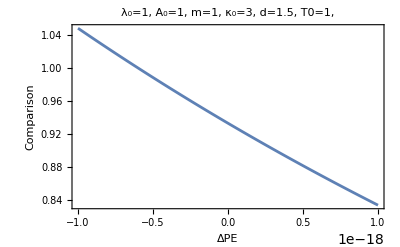

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*m=32.06*1.672621*10^-27; (*Sulfur Mass in kg, 32*Proton mass*)*)
κ0=3;
d=1.2;
T0=60*1.602*10^-19; (*60 eV in Joules*)

Plot[d*(ΔPE/(κ0*T0)+1)^(-1/2-κ0)*(κ0/(2*κ0+1/2))*Hypergeometric2F1[1,κ0+1/2,2*κ0+3/2,1-(d-1)/(ΔPE/(κ0*T0)+1)],{ΔPE,-10^-18,10^-18},Frame->True,FrameLabel->{"ΔPE","Comparison"},PlotLabel->"λ_0=1, A_0=1, m=1, κ_0=3, d=1.5, T0=1,  "]
```

```mathematica
(0/(κ0*T0)+1)^(-1/2-κ0)*(κ0/(2*κ0+0.5))*Hypergeometric2F1[1,κ0+1/2,2*κ0+3/2,1-(d-1)/(0/(κ0*T0)+1)]
```

1.

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
κ0=3;
d=1;
T0=60*1.602*10^-19; (*60 eV in Joules*)

n0*d*(0/(κpar0*Tpar0)+1)^(-1/2-κpar0)*(κ0/(2*κ0+0.5))*Hypergeometric2F1[1,κpar0+0.5,κpar0*(1+λ0)+1.5,1-λ0*A0*(d-1)/(ΔPE/(κpar0*Tpar0)+1)]
```

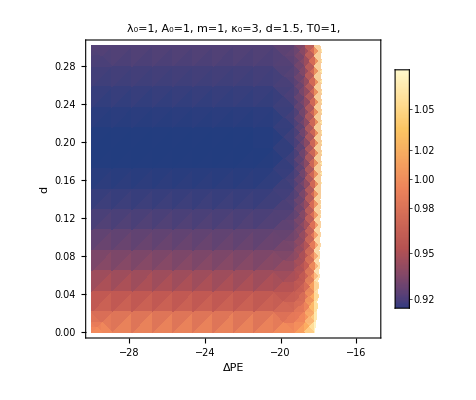

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*m=32.06*1.672621*10^-27; (*Sulfur Mass in kg, 32*Proton mass*)*)
κ0=3;
T0=60*1.602*10^-19; (*60 eV in Joules*)

DensityPlot[d*(-ΔPE/(κ0*T0)+1)^(-1/2-κ0)*(κ0/(2*κ0+1/2))*Hypergeometric2F1[1,κ0+1/2,2*κ0+3/2,1-(d-1)/(-ΔPE/(κ0*T0)+1)],{ΔPE,10^-30,10^-15},{d,1,2},Frame->True,FrameLabel->{"ΔPE","d"},PlotLabel->"λ_0=1, A_0=1, m=1, κ_0=3, d=1.5, T0=1,  ",PlotLegends->Automatic,ScalingFunctions->{"Log10","Log10","Log10"}]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*assumps={Tpar0>0,A0>0,κpar0>0.5,λ0*κpar0>1,λ0>0,d>1,ΔPE∈Reals,ΔPE/(κpar0*Tpar0)>-1,n0>0,m>0};*)
(*n=n0*d*(ΔPE/(κpar0*Tpar0)+1)^(-1/2-κpar0)*((λ0*κpar0)/(κpar0*(λ0+1)+1/2))*Hypergeometric2F1[1,κpar0+1/2,κpar0*(1+λ0)+3/2,1-λ0*A0*(d-1)/(ΔPE/(κpar0*Tpar0)+1)];*)
(*f0 in terms of vperp and vpar =(n0 Gamma[1+κpar0])/(2 √2 A0 π^(3/2) √((Tpar0^3 κpar0)/m^3) Gamma[1/2+κpar0])*(1+(m*vperp^2)/(2*d*A0*λ0*κpar0*Tpar0))^(-1-λ0*κpar0)*(1+(m*vpar^2/2+m*vperp^2/2*(1-1/d)+ΔPE)/(κpar0*Tpar0))^(-1-κpar0);*)
(*f0 in terms of vperp0 and vpar0 =(n0 Gamma[1+κpar0])/(2 √2 A0 π^(3/2) √((Tpar0^3 κpar0)/m^3) Gamma[1/2+κpar0])*(1+(m*vperp0^2)/(2*A0*λ0*κpar0*Tpar0))^(-1-λ0*κpar0)*(1+(m*vpar0^2)/(2*κpar0*Tpar0))^(-1-κpar0);*)
assumps={Tpar>0,A>0,κpar>0.5,λ*κpar>1,λ>0,d>1,ΔPE∈Reals,ΔPE/(κpar*Tpar)>-1,n0>0,m>0};
f=(n Gamma[1+κpar])/(2 √2 A π^(3/2) √((Tpar^3 κpar)/m^3) Gamma[1/2+κpar])*(1+(m*vperp^2)/(2*A*λ*κpar*Tpar))^(-1-λ*κpar)*(1+(m*vpar^2)/(2*κpar*Tpar))^(-1-κpar);
FullSimplify[Integrate[2*Pi*vperp*f,{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]/n,assumps]
FullSimplify[(m^(1/2)/(n √(π/2)))*Integrate[2*Pi*vperp^2*f,{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
FullSimplify[(m^(1/2)/(n √(π/2)))*Integrate[2*Pi*vperp*vpar*f,{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
FullSimplify[m/(2*n)*Integrate[2*Pi*vperp^3*f,{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
FullSimplify[m/n*Integrate[2*Pi*vperp*vpar^2*f,{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
FullSimplify[(m^(3/2)/(3*n √(π/2)))*Integrate[2*Pi*vperp^4*f,{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
FullSimplify[(m^(3/2)/(3*n √(π/2)))*Integrate[2*Pi*vperp*vpar^3*f,{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
FullSimplify[(m^(4/2)/(8*n))*Integrate[2*Pi*vperp^5*f,{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
FullSimplify[(m^(4/2)/(3*n))*Integrate[2*Pi*vperp*vpar^4*f,{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
```

1

(√(A Tpar κpar λ) Gamma[-1/2+κpar λ])/Gamma[κpar λ]

0

(A Tpar κpar λ)/(-1+κpar λ)

(2 Tpar κpar)/(-1+2 κpar)

ConditionalExpression[((A Tpar κpar λ)^(3/2) Gamma[-3/2+κpar λ])/Gamma[κpar λ], 2 κpar λ>3]

0

ConditionalExpression[(A^2 Tpar^2 κpar^2 λ^2)/(2-3 κpar λ+κpar^2 λ^2), κpar λ>2]

(4 Tpar^2 κpar^2)/(3+4 (-2+κpar) κpar)

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*assumps={Tpar0>0,A0>0,κpar0>0.5,λ0*κpar0>1,λ0>0,d>1,ΔPE∈Reals,ΔPE/(κpar0*Tpar0)>-1,n0>0,m>0};*)
(*n=n0*d*(ΔPE/(κpar0*Tpar0)+1)^(-1/2-κpar0)*((λ0*κpar0)/(κpar0*(λ0+1)+1/2))*Hypergeometric2F1[1,κpar0+1/2,κpar0*(1+λ0)+3/2,1-λ0*A0*(d-1)/(ΔPE/(κpar0*Tpar0)+1)];*)
(*f0 in terms of vperp and vpar =(n0 Gamma[1+κpar0])/(2 √2 A0 π^(3/2) √((Tpar0^3 κpar0)/m^3) Gamma[1/2+κpar0])*(1+(m*vperp^2)/(2*d*A0*λ0*κpar0*Tpar0))^(-1-λ0*κpar0)*(1+(m*vpar^2/2+m*vperp^2/2*(1-1/d)+ΔPE)/(κpar0*Tpar0))^(-1-κpar0);*)
(*f0 in terms of vperp0 and vpar0 =(n0 Gamma[1+κpar0])/(2 √2 A0 π^(3/2) √((Tpar0^3 κpar0)/m^3) Gamma[1/2+κpar0])*(1+(m*vperp0^2)/(2*A0*λ0*κpar0*Tpar0))^(-1-λ0*κpar0)*(1+(m*vpar0^2)/(2*κpar0*Tpar0))^(-1-κpar0);*)
assumps={Tpar>0,Tperp>0,A>0,κpar>0.5,κperp>1,d>1,ΔPE∈Reals,ΔPE/(κpar*Tpar)>-1,n0>0,m>0};
f=(n Gamma[1+κpar])/(2 √2 Tperp π^(3/2) √((Tpar κpar)/m^3) Gamma[1/2+κpar])*(1+(m*vperp^2)/(2*κperp*Tperp))^(-1-κperp)*(1+(m*vpar^2)/(2*κpar*Tpar))^(-1-κpar);
FullSimplify[Integrate[2*Pi*vperp*f,{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]/n,assumps]
FullSimplify[(m^(1/2)/(n √(π/2)))*Integrate[2*Pi*vperp^2*f,{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
FullSimplify[(m^(1/2)/(n √(π/2)))*Integrate[2*Pi*vperp*vpar*f,{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
FullSimplify[m/(2*n)*Integrate[2*Pi*vperp^3*f,{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
FullSimplify[m/n*Integrate[2*Pi*vperp*vpar^2*f,{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
FullSimplify[(m^(3/2)/(3*n √(π/2)))*Integrate[2*Pi*vperp^4*f,{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
FullSimplify[(m^(3/2)/(3*n √(π/2)))*Integrate[2*Pi*vperp*vpar^3*f,{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
FullSimplify[(m^(4/2)/(8*n))*Integrate[2*Pi*vperp^5*f,{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
FullSimplify[(m^(4/2)/(3*n))*Integrate[2*Pi*vperp*vpar^4*f,{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
```

1

(√(Tperp κperp) Gamma[-1/2+κperp])/Gamma[κperp]

0

(Tperp κperp)/(-1+κperp)

(2 Tpar κpar)/(-1+2 κpar)

ConditionalExpression[((Tperp κperp)^(3/2) Gamma[-3/2+κperp])/Gamma[κperp], κperp>3/2]

0

ConditionalExpression[(Tperp^2 κperp^2)/(2-3 κperp+κperp^2), κperp>2.]

(4 Tpar^2 κpar^2)/(3+4 (-2+κpar) κpar)

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*assumps={Tpar0>0,A0>0,κpar0>0.5,λ0*κpar0>1,λ0>0,d>1,ΔPE∈Reals,ΔPE/(κpar0*Tpar0)>-1,n0>0,m>0};*)
(*n=n0*d*(ΔPE/(κpar0*Tpar0)+1)^(-1/2-κpar0)*((λ0*κpar0)/(κpar0*(λ0+1)+1/2))*Hypergeometric2F1[1,κpar0+1/2,κpar0*(1+λ0)+3/2,1-λ0*A0*(d-1)/(ΔPE/(κpar0*Tpar0)+1)];*)
(*f0 in terms of vperp and vpar =(n0 Gamma[1+κpar0])/(2 √2 A0 π^(3/2) √((Tpar0^3 κpar0)/m^3) Gamma[1/2+κpar0])*(1+(m*vperp^2)/(2*d*A0*λ0*κpar0*Tpar0))^(-1-λ0*κpar0)*(1+(m*vpar^2/2+m*vperp^2/2*(1-1/d)+ΔPE)/(κpar0*Tpar0))^(-1-κpar0);*)
(*f0 in terms of vperp0 and vpar0 =(n0 Gamma[1+κpar0])/(2 √2 A0 π^(3/2) √((Tpar0^3 κpar0)/m^3) Gamma[1/2+κpar0])*(1+(m*vperp0^2)/(2*A0*λ0*κpar0*Tpar0))^(-1-λ0*κpar0)*(1+(m*vpar0^2)/(2*κpar0*Tpar0))^(-1-κpar0);*)
assumps={Tpar>0,Tperp>0,A>0,κpar>0.5,κperp>1,d>1,ΔPE∈Reals,ΔPE/(κpar*Tpar)>-1,n>0,m>0};
f=n/(2 √2 Tperp π^(3/2) √(Tpar/m^3))*Exp[(-m*vperp^2)/(2*Tperp)]*Exp[-(m*vpar^2)/(2*Tpar)];FullSimplify[Integrate[2*Pi*vperp*f,{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]/n,assumps]
FullSimplify[(m^(1/2)/(n √(π/2)))*Integrate[2*Pi*vperp^2*f,{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
FullSimplify[(m^(1/2)/(n √(π/2)))*Integrate[2*Pi*vperp*vpar*f,{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
FullSimplify[m/(2*n)*Integrate[2*Pi*vperp^3*f,{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
FullSimplify[m/n*Integrate[2*Pi*vperp*vpar^2*f,{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
FullSimplify[(m^(3/2)/(3*n √(π/2)))*Integrate[2*Pi*vperp^4*f,{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
FullSimplify[(m^(3/2)/(3*n √(π/2)))*Integrate[2*Pi*vperp*vpar^3*f,{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
FullSimplify[(m^(4/2)/(8*n))*Integrate[2*Pi*vperp^5*f,{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
FullSimplify[(m^(4/2)/(3*n))*Integrate[2*Pi*vperp*vpar^4*f,{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
```

1

√Tperp

0

Tperp

Tpar

Tperp^(3/2)

0

Tperp^2

Tpar^2

```mathematica
(√(Tperp κperp) Gamma[-1/2+κperp])/Gamma[κperp]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
FullSimplify[Hypergeometric2F1[a,b,c,z]==Hypergeometric2F1[b,a,c,z]]
```

True

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={Tpar0>0,A0>0,κpar0>0.5,λ0*κpar0>1,λ0>0,d>1,ΔPE∈Reals,ΔPE/(κpar0*Tpar0)>-1,n0>0,m>0};
n=n0*d*(ΔPE/(κpar0*Tpar0)+1)^(-1/2-κpar0)*((λ0*κpar0)/(κpar0*(λ0+1)+1/2))*Hypergeometric2F1[1,κpar0+1/2,κpar0*(1+λ0)+3/2,1-λ0*A0*(d-1)/(ΔPE/(κpar0*Tpar0)+1)]


m/(2*n)*2*Pi*(n0 Gamma[1+κpar0])/(2 √2 A0 π^(3/2) √((Tpar0^3 κpar0)/m^3) Gamma[1/2+κpar0])*Integrate[vperp^3*(1+(m*vperp^2)/(2*d*A0*λ0*κpar0*Tpar0))^(-1-λ0*κpar0)*(1+(m*vpar^2/2+m*vperp^2/2*(1-1/d)+ΔPE)/(κpar0*Tpar0))^(-1-κpar0),{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]
m/n*2*Pi*(n0 Gamma[1+κpar0])/(2 √2 A0 π^(3/2) √((Tpar0^3 κpar0)/m^3) Gamma[1/2+κpar0])*Integrate[vperp*vpar^2*(1+(m*vperp^2)/(2*d*A0*λ0*κpar0*Tpar0))^(-1-λ0*κpar0)*(1+(m*vpar^2/2+m*vperp^2/2*(1-1/d)+ΔPE)/(κpar0*Tpar0))^(-1-κpar0),{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]
```

(d n0 (1+ΔPE/(Tpar0 κpar0))^(-1/2-κpar0) κpar0 λ0 Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0 (1+λ0),1-(A0 (-1+d) λ0)/(1+ΔPE/(Tpar0 κpar0))])/(1/2+κpar0 (1+λ0))

(d √(d/m) Tpar0^2 (1+ΔPE/(Tpar0 κpar0))^(1/2+κpar0) κpar0 (d Tpar0 κpar0)^κpar0 (d (ΔPE+Tpar0 κpar0))^(-1/2-κpar0) (1/2+κpar0 (1+λ0)) (1/(Gamma[1/2+κpar0] Gamma[κpar0 λ0])(-1+d)^(-1+κpar0 λ0) π (ΔPE+Tpar0 κpar0)^(1/2+κpar0) (A0 (-1+d) Tpar0 (-1+2 κpar0)+2 (ΔPE+Tpar0 κpar0)) (A0 Tpar0 κpar0 λ0)^(κpar0 λ0) (ΔPE+Tpar0 κpar0 (1+A0 (λ0-d λ0)))^(-1/2-κpar0 (1+λ0)) Csc[π κpar0 λ0] Gamma[-1/2+κpar0+κpar0 λ0]+(A0 Tpar0 (2 (ΔPE+Tpar0 κpar0) (-1+κpar0 λ0)-κpar0 (A0 (-1+d) Tpar0 (-1+2 κpar0)+2 (ΔPE+Tpar0 κpar0)) λ0 Hypergeometric2F1[1,1/2+κpar0,2-κpar0 λ0,(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)]))/((-1+κpar0 λ0) (-ΔPE+Tpar0 κpar0 (-1+A0 (-1+d) λ0)))))/(2 m √((Tpar0^3 κpar0)/m^3) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0 (1+λ0),1-(A0 (-1+d) λ0)/(1+ΔPE/(Tpar0 κpar0))])

-((Tpar0^2 (1+ΔPE/(Tpar0 κpar0))^(1/2+κpar0) (Tpar0 κpar0)^κpar0 (1/2+κpar0 (1+λ0)) (π κpar0 λ0 (A0 (-1+d) Tpar0 κpar0 λ0)^(κpar0 λ0) (ΔPE+Tpar0 κpar0 (1+A0 λ0-A0 d λ0))^(1/2-κpar0 (1+λ0)) Csc[π κpar0 λ0] Gamma[-1/2+κpar0+κpar0 λ0]-(ΔPE+Tpar0 κpar0)^(1/2-κpar0) Gamma[-1/2+κpar0] Gamma[1+κpar0 λ0] Hypergeometric2F1[1,-1/2+κpar0,1-κpar0 λ0,(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)]))/(m^(3/2) √((Tpar0^3 κpar0)/m^3) λ0 Gamma[1/2+κpar0] Gamma[1+κpar0 λ0] Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0 (1+λ0),1-(A0 (-1+d) λ0)/(1+ΔPE/(Tpar0 κpar0))]))

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={Tpar0>0,A0>0,κpar0>0.5,λ0*κpar0>1,λ0>0,d>1,ΔPE∈Reals,ΔPE/(κpar0*Tpar0)>-1,n0>0,m>0};
FullSimplify[(d √(d/m) Tpar0^2 (1+ΔPE/(Tpar0 κpar0))^(1/2+κpar0) κpar0 (d Tpar0 κpar0)^κpar0 (d (ΔPE+Tpar0 κpar0))^(-1/2-κpar0) (1/2+κpar0 (1+λ0)) (1/(Gamma[1/2+κpar0] Gamma[κpar0 λ0])(-1+d)^(-1+κpar0 λ0) π (ΔPE+Tpar0 κpar0)^(1/2+κpar0) (A0 (-1+d) Tpar0 (-1+2 κpar0)+2 (ΔPE+Tpar0 κpar0)) (A0 Tpar0 κpar0 λ0)^(κpar0 λ0) (ΔPE+Tpar0 κpar0 (1+A0 (λ0-d λ0)))^(-1/2-κpar0 (1+λ0)) Csc[π κpar0 λ0] Gamma[-1/2+κpar0+κpar0 λ0]+(A0 Tpar0 (2 (ΔPE+Tpar0 κpar0) (-1+κpar0 λ0)-κpar0 (A0 (-1+d) Tpar0 (-1+2 κpar0)+2 (ΔPE+Tpar0 κpar0)) λ0 Hypergeometric2F1[1,1/2+κpar0,2-κpar0 λ0,(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)]))/((-1+κpar0 λ0) (-ΔPE+Tpar0 κpar0 (-1+A0 (-1+d) λ0)))))/(2 m √((Tpar0^3 κpar0)/m^3) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0 (1+λ0),1-(A0 (-1+d) λ0)/(1+ΔPE/(Tpar0 κpar0))]),assumps]
FullSimplify[-((Tpar0^2 (1+ΔPE/(Tpar0 κpar0))^(1/2+κpar0) (Tpar0 κpar0)^κpar0 (1/2+κpar0 (1+λ0)) (π κpar0 λ0 (A0 (-1+d) Tpar0 κpar0 λ0)^(κpar0 λ0) (ΔPE+Tpar0 κpar0 (1+A0 λ0-A0 d λ0))^(1/2-κpar0 (1+λ0)) Csc[π κpar0 λ0] Gamma[-1/2+κpar0+κpar0 λ0]-(ΔPE+Tpar0 κpar0)^(1/2-κpar0) Gamma[-1/2+κpar0] Gamma[1+κpar0 λ0] Hypergeometric2F1[1,-1/2+κpar0,1-κpar0 λ0,(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)]))/(m^(3/2) √((Tpar0^3 κpar0)/m^3) λ0 Gamma[1/2+κpar0] Gamma[1+κpar0 λ0] Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0 (1+λ0),1-(A0 (-1+d) λ0)/(1+ΔPE/(Tpar0 κpar0))])),assumps]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={Tpar0>0,A0>0,κpar0>0.5,λ0*κpar0>1,λ0>0,d>1,ΔPE∈Reals,ΔPE/(κpar0*Tpar0)>-1,n0>0,m>0};
FullSimplify[Hypergeometric2F1[1,κpar0+1/2,κpar0*(1+λ0)+3/2,1-λ0*A0*(d-1)/(ΔPE/(κpar0*Tpar0)+1)]/Hypergeometric2F1[2,κpar0+1/2,κpar0*(1+λ0)+3/2,1-λ0*A0*(d-1)/(ΔPE/(κpar0*Tpar0)+1)],assumps]
```

Remove::rmnsm: There are no symbols matching "Global`*".

Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)]/Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
FullSimplify[Hypergeometric2F1[1,b,c,z]/Hypergeometric2F1[2,b,c,z],assumps]
```

Hypergeometric2F1[1,b,c,z]/Hypergeometric2F1[2,b,c,z]

```mathematica
(m^(0.5)/(((Pi/2)^(0.5))*n))
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={Tpar0>0,A0>0,κpar0>0.5,λ0*κpar0>1,λ0>0,d>1,ΔPE∈Reals,ΔPE/(κpar0*Tpar0)>-1,n0>0,m>0};
FullSimplify[(m*(2*Pi)/(2 √2 A0 π^(3/2) √((Tpar0^3 κpar0)/m^3) Gamma[1/2+κpar0])*(2*(κpar0*Tpar0)/m)^(3/2)*Sqrt[Pi]*Gamma[-1/2+κpar0]*(κpar0*Tpar0)/m*A0)/κpar0,assumps]
```

(4 Tpar0 κpar0)/(-1+2 κpar0)

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={Tpar0>0,A0>0,κpar0>0.5,λ0*κpar0>1,λ0>0,d>1,ΔPE∈Reals,ΔPE/(κpar0*Tpar0)>-1,n0>0,m>0,λ>0,A>0};
(*FullSimplify[d*A0*λ0*κpar0*Tpar0*(κpar0*(λ0+1)+1/2)*Gamma[(λ0+1)*κpar0-1/2]/Gamma[(λ0+1)*κpar0+3/2]*Hypergeometric2F1[2,κpar0+1/2,κpar0*(1+λ0)+3/2,1-λ0*A0*(d-1)/(ΔPE/(κpar0*Tpar0)+1)]/Hypergeometric2F1[1,κpar0+1/2,κpar0*(1+λ0)+3/2,1-λ0*A0*(d-1)/(ΔPE/(κpar0*Tpar0)+1)],assumps]
FullSimplify[(d*A0*λ0*κpar0*Tpar0)^(1/2)*(κpar0*(λ0+1)+1/2)*Gamma[(λ0+1)*κpar0]/Gamma[(λ0+1)*κpar0+3/2]*Hypergeometric2F1[3/2,κpar0+1/2,κpar0*(1+λ0)+3/2,1-λ0*A0*(d-1)/(ΔPE/(κpar0*Tpar0)+1)]/Hypergeometric2F1[1,κpar0+1/2,κpar0*(1+λ0)+3/2,1-λ0*A0*(d-1)/(ΔPE/(κpar0*Tpar0)+1)],assumps]*)
Solve[{(√(Tperp κperp) Gamma[-1/2+κperp])/Gamma[κperp]==(√(A0 d Tpar0 κpar0 λ0) Gamma[κpar0+κpar0 λ0] Hypergeometric2F1[3/2,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)])/(Gamma[1/2+κpar0+κpar0 λ0] Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)]),(Tperp κperp)/(-1+κperp)==(2 A0 d Tpar0 κpar0 λ0 Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)])/((-1+2 κpar0 (1+λ0)) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)])},{Tperp,κperp},Assumptions->assumps]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[{(√(Tperp κperp) Gamma[-1/2+κperp])/Gamma[κperp]==(√(A0 d Tpar0 κpar0 λ0) Gamma[κpar0+κpar0 λ0] Hypergeometric2F1[3/2,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)])/(Gamma[1/2+κpar0+κpar0 λ0] Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)]),(Tperp κperp)/(-1+κperp)==(2 A0 d Tpar0 κpar0 λ0 Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)])/((-1+2 κpar0 (1+λ0)) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)])},{Tperp,κperp},Assumptions→{Tpar0>0,A0>0,κpar0>0.5,κpar0 λ0>1,λ0>0,d>1,ΔPE∈ℝ,ΔPE/(Tpar0 κpar0)>-1,n0>0,m>0,λ>0,A>0}]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={α>0,β>0};

(*Tperp==β*(-1+κperp)/κperp*)
(*G = α/Sqrt[β]*)

Reduce[G>0&&(√(-1+κperp)*Gamma[-1/2+κperp])/Gamma[κperp]==G,{Tperp,κperp},PositiveReals]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[G>0&&(√(-1+κperp) Gamma[-1/2+κperp])/Gamma[κperp]==G,{Tperp,κperp},]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={Tpar0>0,A0>0,κpar0>0.5,λ0*κpar0>1,λ0>0,d>1,ΔPE∈Reals,ΔPE/(κpar0*Tpar0)>-1,n0>0,m>0};
FullSimplify[1/(d*((λ0*κpar0)/(κpar0*(λ0+1)+1/2))*Hypergeometric2F1[1,κpar0+1/2,κpar0*(1+λ0)+3/2,1-λ0*A0*(d-1)/(ΔPE/(κpar0*Tpar0)+1)])(m^(4/2)/8*(2*Pi)/(2 √2 A0 π^(3/2) √((Tpar0^3 κpar0)/m^3))*Sqrt[Pi]*(2*(κpar0*Tpar0)/m)^(7/2)*1/2*(2*Gamma[κpar0*(1+λ0)-3/2]/Gamma[κpar0*(1+λ0)+3/2])*(d*A0*λ0)^3*Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)]),assumps]
```

(4 A0^2 d^2 Tpar0^2 κpar0^2 λ0^2 Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)])/((-3+2 κpar0 (1+λ0)) (-1+2 κpar0 (1+λ0)) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)])

```mathematica
(*n=n0*d*(ΔPE/(κpar0*Tpar0)+1)^(-1/2-κpar0)*((λ0*κpar0)/(κpar0*(λ0+1)+1/2))*Hypergeometric2F1[1,κpar0+1/2,κpar0*(1+λ0)+3/2,1-λ0*A0*(d-1)/(ΔPE/(κpar0*Tpar0)+1)];*)
(*f0 in terms of vperp and vpar =(n0 Gamma[1+κpar0])/(2 √2 A0 π^(3/2) √((Tpar0^3 κpar0)/m^3) Gamma[1/2+κpar0])*(1+(m*vperp^2)/(2*d*A0*λ0*κpar0*Tpar0))^(-1-λ0*κpar0)*(1+(m*vpar^2/2+m*vperp^2/2*(1-1/d)+ΔPE)/(κpar0*Tpar0))^(-1-κpar0);*)
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={Tpar0>0,A0>0,κpar0>0.5,λ0*κpar0>1,λ0>0,d>1,ΔPE∈Reals,ΔPE/(κpar0*Tpar0)>-1,n0>0,m>0,λ>0,A>0};
(*FullSimplify[d*A0*λ0*κpar0*Tpar0*(κpar0*(λ0+1)+1/2)*Gamma[(λ0+1)*κpar0-1/2]/Gamma[(λ0+1)*κpar0+3/2]*Hypergeometric2F1[2,κpar0+1/2,κpar0*(1+λ0)+3/2,1-λ0*A0*(d-1)/(ΔPE/(κpar0*Tpar0)+1)]/Hypergeometric2F1[1,κpar0+1/2,κpar0*(1+λ0)+3/2,1-λ0*A0*(d-1)/(ΔPE/(κpar0*Tpar0)+1)],assumps]
FullSimplify[(d*A0*λ0*κpar0*Tpar0)^(1/2)*(κpar0*(λ0+1)+1/2)*Gamma[(λ0+1)*κpar0]/Gamma[(λ0+1)*κpar0+3/2]*Hypergeometric2F1[3/2,κpar0+1/2,κpar0*(1+λ0)+3/2,1-λ0*A0*(d-1)/(ΔPE/(κpar0*Tpar0)+1)]/Hypergeometric2F1[1,κpar0+1/2,κpar0*(1+λ0)+3/2,1-λ0*A0*(d-1)/(ΔPE/(κpar0*Tpar0)+1)],assumps]*)
FullSimplify[Solve[{(Tperp^2 κperp^2)/(2-3 κperp+κperp^2)==(4 A0^2 d^2 Tpar0^2 κpar0^2 λ0^2 Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)])/((-3+2 κpar0 (1+λ0)) (-1+2 κpar0 (1+λ0)) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)]),(Tperp κperp)/(-1+κperp)==(2 A0 d Tpar0 κpar0 λ0 Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)])/((-1+2 κpar0 (1+λ0)) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)])},{Tperp,κperp},Assumptions->assumps],assumps]
```

{{Tperp→(2 A0 d Tpar0 κpar0 λ0 Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)])/((3-2 κpar0 (1+λ0)) Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)]^2+2 (-1+2 κpar0 (1+λ0)) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)]),κperp→((3-2 κpar0 (1+λ0)) Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)]^2+2 (-1+2 κpar0 (1+λ0)) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)])/((3-2 κpar0 (1+λ0)) Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)]^2+(-1+2 κpar0 (1+λ0)) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)])}}

```mathematica
%90/.Rule->Equal
```

{{Tperp==(2 A0 d Tpar0 κpar0 λ0 Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)])/((3-2 κpar0 (1+λ0)) Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)]^2+2 (-1+2 κpar0 (1+λ0)) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)]),κperp==((3-2 κpar0 (1+λ0)) Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)]^2+2 (-1+2 κpar0 (1+λ0)) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)])/((3-2 κpar0 (1+λ0)) Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)]^2+(-1+2 κpar0 (1+λ0)) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κpar0 λ0,1-(A0 (-1+d) Tpar0 κpar0 λ0)/(ΔPE+Tpar0 κpar0)])}}

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
FullSimplify[1/2*((T κ)/(-1+κ)+(2 T κ)/(-1+2 κ)),{κ>1.5,T>0}]
```

(T κ (-3+4 κ))/(2-6 κ+4 κ^2)

```mathematica
Gamma[2]
```

1

```mathematica
Gamma[3]
```

2

```mathematica
Gamma[3/2]
```

(√π)/2

```mathematica
m/n*2*Pi*(n0 Gamma[1+κpar0])/(2 √2  π^(3/2)*Tperp* √((Tpar0 κpar0)/m^3) Gamma[1/2+κpar0])*Integrate[vperp*vpar^2*(1+(B0*m*vperp^2)/(2*B*κperp0*Tperp0))^(-1-κperp0)*(1+(m*vpar^2/2+m*vperp^2/2*(1-B0/B)+ΔPE)/(κpar0*Tpar0))^(-1-κpar0),{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps]
 n=n0*B/B0*(ΔPE/(κpar0*Tpar0)+1)^(-1/2-κpar0)*(κperp0/(κperp0+κpar0+1/2))*Hypergeometric2F1[1,κpar0+1/2,κperp0+κpar0+3/2,1-δ]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={Tpar0>0,κpar0>1/2,d>1,ΔPE∈Reals,ΔPE/(κpar0*Tpar0)>-1,m>0,vperp>=0};
Integrate[vpar^2*(1+(m*vpar^2/2+m*vperp^2/2*(1-1/d)+ΔPE)/(κpar0*Tpar0))^(-1-κpar0),{vpar,-Infinity,Infinity},Assumptions->assumps]
```

(2^κpar0 √π Tpar0 κpar0 (Tpar0 κpar0)^κpar0 (d/((-1+d) m vperp^2+2 d (ΔPE+Tpar0 κpar0)))^(-1/2+κpar0) Gamma[-1/2+κpar0])/(m^(3/2) Gamma[1+κpar0])

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={Tpar0>0,κpar0>1/2,d>1,ΔPE∈Reals,ΔPE/(κpar0*Tpar0)>-1,m>0};
FullSimplify[(2^κpar0 √π Tpar0 κpar0 (Tpar0 κpar0)^κpar0 (d/((-1+d) m vperp^2+2 d (ΔPE+Tpar0 κpar0)))^(-1/2+κpar0) Gamma[-1/2+κpar0])/(m^(3/2) Gamma[1+κpar0]),assumps]
```

(2^κpar0 √π Tpar0 κpar0 (Tpar0 κpar0)^κpar0 (d/((-1+d) m vperp^2+2 d (ΔPE+Tpar0 κpar0)))^(-1/2+κpar0) Gamma[-1/2+κpar0])/(m^(3/2) Gamma[1+κpar0])

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={Tpar0>0,κpar0>1/2,d>1,ΔPE∈Reals,ΔPE/(κpar0*Tpar0)>-1,m>0,δ>0};
n=n0*B/B0*(ΔPE/(κpar0*Tpar0)+1)^(-1/2-κpar0)*(κperp0/(κperp0+κpar0+1/2))*Hypergeometric2F1[1,κpar0+1/2,κperp0+κpar0+3/2,1-δ];
c0=(m^(3/2) n0 Gamma[1+κpar0])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κpar0) Gamma[1/2+κpar0]);
FullSimplify[(m/n)*(2*Pi*c0)*(2^κpar0 √π Tpar0 κpar0 (Tpar0 κpar0)^κpar0 (2  (ΔPE+Tpar0 κpar0))^(1/2-κpar0) Gamma[-1/2+κpar0])/(m^(3/2) Gamma[1+κpar0])*Hypergeometric2F1[1,κpar0-1/2,κperp0+κpar0+1/2,1-δ]/(2*(κpar0+κperp0-1/2)),assumps]
```

(2 B0 m (ΔPE+Tpar0 κpar0) Hypergeometric2F1Regularized[1,-1/2+κpar0,1/2+κpar0+κperp0,1-δ])/(B Tperp0 (-1+2 κpar0) κperp0 (-1+2 κpar0+2 κperp0) Hypergeometric2F1Regularized[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ])

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={Tpar0>0,κpar0>1/2,d>1,ΔPE∈Reals,ΔPE/(κpar0*Tpar0)>-1,m>0,vperp>=0};
FullSimplify[Integrate[vpar^4*(1+(m*vpar^2/2+m*vperp^2/2*(1-1/d)+ΔPE)/(κpar0*Tpar0))^(-1-κpar0),{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
```

ConditionalExpression[(3 2^(-1+κpar0) √π Tpar0 κpar0 (d Tpar0 κpar0)^κpar0 ((-1+d) m vperp^2+2 d (ΔPE+Tpar0 κpar0))^(3/2-κpar0) Gamma[-3/2+κpar0])/(d^(3/2) m^(5/2) Gamma[1+κpar0]), κpar0>3/2]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={Tpar0>0,κpar0>3/2,d>1,ΔPE∈Reals,ΔPE/(κpar0*Tpar0)>-1,m>0,δ>0};
n=n0*B/B0*(ΔPE/(κpar0*Tpar0)+1)^(-1/2-κpar0)*(κperp0/(κperp0+κpar0+1/2))*Hypergeometric2F1[1,κpar0+1/2,κperp0+κpar0+3/2,1-δ];
c0=(m^(3/2) n0 Gamma[1+κpar0])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κpar0) Gamma[1/2+κpar0]);
FullSimplify[(m^2/(3*n))*(2*Pi*c0)*(3 2^(-1+κpar0) √π Tpar0 κpar0 (d Tpar0 κpar0)^κpar0 (2 d (ΔPE+Tpar0 κpar0))^(3/2-κpar0) Gamma[-3/2+κpar0])/(d^(3/2) m^(5/2) Gamma[1+κpar0])*Hypergeometric2F1[1,κpar0-3/2,κperp0+κpar0-1/2,1-δ]/(2*(κpar0+κperp0-3/2)),assumps]
```

(2 B0 m (ΔPE+Tpar0 κpar0)^2 (1+2 κpar0+2 κperp0) Hypergeometric2F1[1,-3/2+κpar0,-1/2+κpar0+κperp0,1-δ])/(B Tperp0 (3+4 (-2+κpar0) κpar0) κperp0 (-3+2 κpar0+2 κperp0) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ])

True